# Problem 4

## 1. a Gaussian model with μ as the unknown parameter in the log - likelihood function and with a fixed standard deviation of σ = 3

```mathematica
f[μ_]:=LogLikelihood[NormalDistribution[μ,3], {4, 15, 6, 8, 9, 12, 10, 6, 9, 7}]
D[f[μ],μ]
```

1/9 (86-10 μ)

μ=8.6, Get the ML. Set Plot Range [1.72, 17.2]

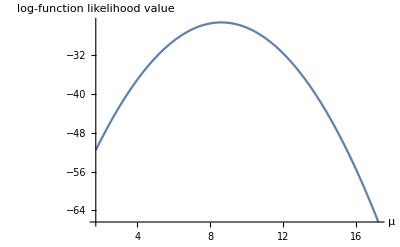

```mathematica
Plot[f[μ],{μ,0.2*8.6,8.6*2},AxesLabel->{μ,log-likelihood function value}]
```

## 2. a uniform distribution with a = 2 and b as the unknown parameter in the log - likelihood function

```mathematica
f[b_]:= LogLikelihood[UniformDistribution[{2,b}], {4, 15, 6, 8, 9, 12, 10, 6, 9, 7}]
D[f[b],b]
```

Piecewise[{{0, b<15}, {-10/(-2+b), b>15}, {Indeterminate, True}}]

b<= 15, get the ML, Set Plot Range [3,30]

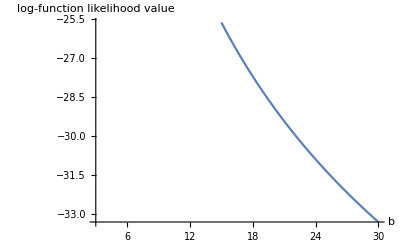

```mathematica
Plot[f[b],{b,3,30},AxesLabel->{b,log-likelihood function value}]
```

## 3. an exponential distribution with the exponential parameter as the unknown parameter in the log - likelihood function.

```mathematica
f[e_]:= LogLikelihood[ExponentialDistribution[e], {4, 15, 6, 8, 9, 12, 10, 6, 9, 7}]
MaxValue[D[f[e],e],e]
```

∞

e=∞ , get the ML, Set Plot Range (-∞,∞ )

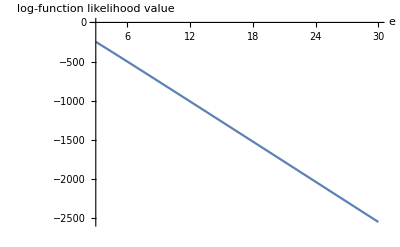

```mathematica
Plot[f[e],{e,3,30},AxesLabel->{e,log-likelihood function value}]
```

# Problem5

```mathematica
EstimatedDistribution[x,NormalDistribution[μ,σ^2],μ]//Timing
```

EstimatedDistribution::insffdt: There is insufficient data to proceed with the computation. The data must contain at least 1 elements.

{0.005587,EstimatedDistribution[x,NormalDistribution[μ,σ^2],μ]}

```mathematica
f[a_,b_]:=1/(b-a)
D[f[a,b],b]
```

-1/(-a+b)^2